```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["64_cv.dat","Table"];
MagnetData = Import["64_magnetization.dat","Table"];
SusceptData = Import["64_susceptibility.dat","Table"];
```

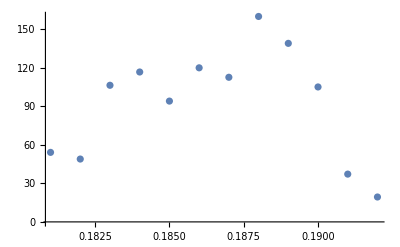

```mathematica
ListPlot[Take[SusceptData,{132,143}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{133,143}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,150},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{138.613 ⅇ^(-41566.9 (-0.186708+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 138.613 | 14.5475 | 9.52831 | 0.0000121609
Sigma | -0.00346826 | 0.000542708 | -6.39066 | 0.000211226
mu | 0.186708 | 0.000432866 | 431.329 | 9.34718×10^-19}

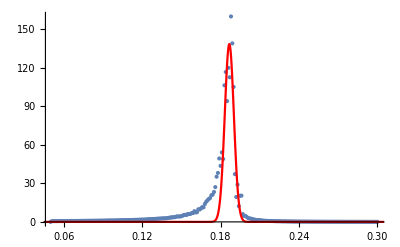

```mathematica
Show[ListPlot[SusceptData,PlotRange->Full],Plot[SusceptFit[x],{x,0,0.4},PlotRange->{{0,0.4},{0,500}}, PlotStyle->Red]]
```

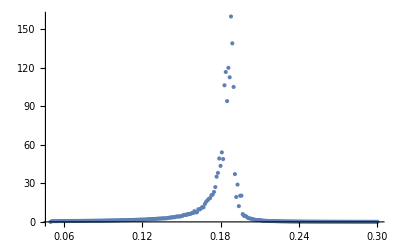

```mathematica
ListPlot[SusceptData,PlotRange->Full]
```